```mathematica
Weibull:
```

```mathematica
ClearAll[α,σ,μ,x]
```

```mathematica
p = k/λ ⅇ^(-((x-μ)/λ)^k)((x-μ)/λ)^(k-1)
```

(ⅇ^(-((x-μ)/λ)^k) k ((x-μ)/λ)^(-1+k))/λ

```mathematica
θ = k;
```

```mathematica
ss = FullSimplify[D[Log[p],θ]]
```

(1-k (-1+((x-μ)/λ)^k) Log[(x-μ)/λ])/k

```mathematica
ss' = FullSimplify[D[ss,θ]]
```

-1/k^2-((x-μ)/λ)^k Log[(x-μ)/λ]^2

```mathematica
csIntCitatel1 = FullSimplify[p^(1+α)*ss]
```

(((ⅇ^(-((x-μ)/λ)^k) k ((x-μ)/λ)^(-1+k))/λ)^(1+α) (1-k (-1+((x-μ)/λ)^k) Log[(x-μ)/λ]))/k

```mathematica
csIntCitatel2 = FullSimplify[csIntCitatel1/.(x-μ)-> y*λ]
```

(((ⅇ^(-y^k) k y^(-1+k))/λ)^(1+α) (1-k (-1+y^k) Log[y]))/k

```mathematica
csIntCitatel3 = FullSimplify[csIntCitatel2*λ/.y-> t^(1/k)]
```

(((ⅇ^(-(t^(1/k))^k) k (t^(1/k))^(-1+k))/λ)^(1+α) λ (1-k (-1+(t^(1/k))^k) Log[t^(1/k)]))/k

```mathematica
csIntCitatel4 = FullSimplify[csIntCitatel3/k*t^((1-k)/k),{k>0,t>0,λ>0,α>0}]
```

(ⅇ^-t ((ⅇ^-t k t^((-1+k)/k))/λ)^α (1+Log[t]-t Log[t]))/k

```mathematica
csIntCitatel5 = FullSimplify[Integrate[csIntCitatel4,{t,0,∞}]]
```

ConditionalExpression[(α (1+α)^(-2+(-1+1/k) α) (k/λ)^α Gamma[1+α-α/k] (k-Log[1+α]+PolyGamma[0,1+α-α/k]))/k^2,Re[(-1+1/k) α]<1&&Re[((-1+k) α)/k]≥-1&&Re[α]>-1]

```mathematica
csIntJmenovatel1 = FullSimplify[p^(1+α)]
```

((ⅇ^(-((x-μ)/λ)^k) k ((x-μ)/λ)^(-1+k))/λ)^(1+α)

```mathematica
csIntJmenovatel2 = FullSimplify[csIntJmenovatel1/.(x-μ)-> y*λ]
```

((ⅇ^(-y^k) k y^(-1+k))/λ)^(1+α)

```mathematica
csIntJmenovatel3 = FullSimplify[csIntJmenovatel2*λ/.y-> t^(1/k)]
```

((ⅇ^(-(t^(1/k))^k) k (t^(1/k))^(-1+k))/λ)^(1+α) λ

```mathematica
csIntJmenovatel4 = FullSimplify[csIntJmenovatel3/k*t^((1-k)/k),{k>0,t>0,λ>0,α>0}]
```

ⅇ^-t ((ⅇ^-t k t^((-1+k)/k))/λ)^α

```mathematica
csIntJmenovatel5 = FullSimplify[Integrate[csIntJmenovatel4,{t,0,∞}]]
```

ConditionalExpression[(1+α)^(-1+(-1+1/k) α) (k/λ)^α Gamma[1+α-α/k],Re[(-1+1/k) α]<1&&Re[α]>-1]

```mathematica
cs = FullSimplify[csIntCitatel5/csIntJmenovatel5]
```

ConditionalExpression[(α (k-Log[1+α]+PolyGamma[0,1+α-α/k]))/(k^2 (1+α)),Re[(-1+1/k) α]<1&&Re[((-1+k) α)/k]≥-1&&Re[α]>-1]

```mathematica
cs' = FullSimplify[D[cs,θ]]
```

ConditionalExpression[(α (-k (k-2 Log[1+α]+2 PolyGamma[0,1+α-α/k])+α PolyGamma[1,1+α-α/k]))/(k^4 (1+α)),Re[(-1+1/k) α]<1&&Re[((-1+k) α)/k]≥-1&&Re[α]>-1]

```mathematica
Ia =FullSimplify[ (ss' - cs'-α(ss-cs)(cs-ss))*p^(1+α)]
```

ConditionalExpression[((ⅇ^(-((x-μ)/λ)^k) k ((x-μ)/λ)^(-1+k))/λ)^(1+α) (-1/k^2-((x-μ)/λ)^k Log[(x-μ)/λ]^2+(α (-α Log[1+α]+k (-1+k (1+α) (-1+((x-μ)/λ)^k) Log[(x-μ)/λ])+α PolyGamma[0,1+α-α/k])^2)/(k^4 (1+α)^2)+(α (k (k-2 Log[1+α]+2 PolyGamma[0,1+α-α/k])-α PolyGamma[1,1+α-α/k]))/(k^4 (1+α))),Re[(-1+1/k) α]<1&&Re[((-1+k) α)/k]≥-1&&Re[α]>-1]

```mathematica
Ia1 = FullSimplify[Ia/.(x-μ)->y*λ]
```

ConditionalExpression[((ⅇ^(-y^k) k y^(-1+k))/λ)^(1+α) (-1/k^2-y^k Log[y]^2+(α (k (-1+k (-1+y^k) (1+α) Log[y])-α Log[1+α]+α PolyGamma[0,1+α-α/k])^2)/(k^4 (1+α)^2)+(α (k (k-2 Log[1+α]+2 PolyGamma[0,1+α-α/k])-α PolyGamma[1,1+α-α/k]))/(k^4 (1+α))),Re[(-1+1/k) α]<1&&Re[((-1+k) α)/k]≥-1&&Re[α]>-1]

```mathematica
Ia2 = FullSimplify[Ia1*λ/.y-> t^(1/k)]
```

ConditionalExpression[((ⅇ^(-(t^(1/k))^k) k (t^(1/k))^(-1+k))/λ)^(1+α) λ (-1/k^2-(t^(1/k))^k Log[t^(1/k)]^2+(α (k (-1+k (-1+(t^(1/k))^k) (1+α) Log[t^(1/k)])-α Log[1+α]+α PolyGamma[0,1+α-α/k])^2)/(k^4 (1+α)^2)+(α (k (k-2 Log[1+α]+2 PolyGamma[0,1+α-α/k])-α PolyGamma[1,1+α-α/k]))/(k^4 (1+α))),Re[(-1+1/k) α]<1&&Re[((-1+k) α)/k]≥-1&&Re[α]>-1]

```mathematica
Ia3 = FullSimplify[Ia2/k*t^((1-k)/k),{k>0,t>0,λ>0,α>0}]
```

ConditionalExpression[1/k^5 t^(-1+1/k) ((ⅇ^-t k t^((-1+k)/k))/λ)^(1+α) λ (-k^2-k^2 t Log[t]^2+(α (k-k (-1+t) (1+α) Log[t]+α Log[1+α]-α PolyGamma[0,1+α-α/k])^2)/(1+α)^2+(α (k (k-2 Log[1+α]+2 PolyGamma[0,1+α-α/k])-α PolyGamma[1,1+α-α/k]))/(1+α)),k+k α>α]

```mathematica
Ia4 = FullSimplify[Integrate[Ia3,{t,0,∞}]]
```

ConditionalExpression[-1/k^4(1+α)^(-3+(-1+1/k) α) (k/λ)^α Gamma[1+α-α/k] (k (k+Log[1+α] (-2 k+2 α+(k+(-1+k) α) Log[1+α]))-2 k (-k+α+(k+(-1+k) α) Log[1+α]) PolyGamma[0,1+α-α/k]+k (k+(-1+k) α) PolyGamma[0,1+α-α/k]^2+(k^2+(-1+k) k α+α^2) PolyGamma[1,1+α-α/k]),k+k α>α&&α>-1&&k>0]

```mathematica
IF = FullSimplify[-Ia4^(-1) * (p^α)*(ss-cs)]
```

ConditionalExpression[(k^2 (1+α)^(2+α-α/k) (1/λ)^-α ((ⅇ^(-((x-μ)/λ)^k) ((x-μ)/λ)^(-1+k))/λ)^α (α Log[1+α]+k (1-k (1+α) (-1+((x-μ)/λ)^k) Log[(x-μ)/λ])-α PolyGamma[0,1+α-α/k]))/(Gamma[1+α-α/k] (k (k+Log[1+α] (-2 k+2 α+(k+(-1+k) α) Log[1+α]))-2 k (-k+α+(k+(-1+k) α) Log[1+α]) PolyGamma[0,1+α-α/k]+k (k+(-1+k) α) PolyGamma[0,1+α-α/k]^2+(k^2+(-1+k) k α+α^2) PolyGamma[1,1+α-α/k])),k>0&&1+α>0&&α<k+k α]

```mathematica
IF1 = FullSimplify[IF/.μ->0]
```

ConditionalExpression[(k^2 (1+α)^(2+α-α/k) ((ⅇ^(-(x/λ)^k) (x/λ)^k)/x)^α (1/λ)^-α (α Log[1+α]+k (1-k (1+α) (-1+(x/λ)^k) Log[x/λ])-α PolyGamma[0,1+α-α/k]))/(Gamma[1+α-α/k] (k (k+Log[1+α] (-2 k+2 α+(k+(-1+k) α) Log[1+α]))-2 k (-k+α+(k+(-1+k) α) Log[1+α]) PolyGamma[0,1+α-α/k]+k (k+(-1+k) α) PolyGamma[0,1+α-α/k]^2+(k^2+(-1+k) k α+α^2) PolyGamma[1,1+α-α/k])),k>0&&1+α>0&&α<k+k α]

```mathematica
IF2 = FullSimplify[IF1/.λ->1]
```

ConditionalExpression[(k^2 (ⅇ^(-x^k) x^(-1+k))^α (1+α)^(2+α-α/k) (k-k^2 (-1+x^k) (1+α) Log[x]+α Log[1+α]-α PolyGamma[0,1+α-α/k]))/(Gamma[1+α-α/k] (k (k+Log[1+α] (-2 k+2 α+(k+(-1+k) α) Log[1+α]))-2 k (-k+α+(k+(-1+k) α) Log[1+α]) PolyGamma[0,1+α-α/k]+k (k+(-1+k) α) PolyGamma[0,1+α-α/k]^2+(k^2+(-1+k) k α+α^2) PolyGamma[1,1+α-α/k])),k>0&&1+α>0&&α<k+k α]

```mathematica
IFun = Function[{k,α} ,(k^2 (ⅇ^(-x^k) x^(-1+k))^α (1+α)^(2+α-α/k) (k-k^2 (-1+x^k) (1+α) Log[x]+α Log[1+α]-α PolyGamma[0,1+α-α/k]))/(Gamma[1+α-α/k] (k (k+Log[1+α] (-2 k+2 α+(k+(-1+k) α) Log[1+α]))-2 k (-k+α+(k+(-1+k) α) Log[1+α]) PolyGamma[0,1+α-α/k]+k (k+(-1+k) α) PolyGamma[0,1+α-α/k]^2+(k^2+(-1+k) k α+α^2) PolyGamma[1,1+α-α/k]))];
```

```mathematica
Needs["PlotLegends`"]
```

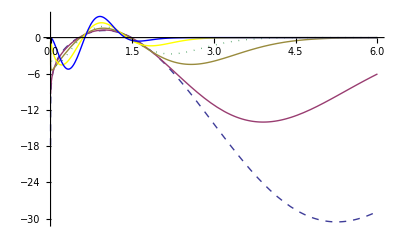

```mathematica
Plot[{
IFun[2,0.05],
IFun[2,0.1],
IFun[2,0.3],
IFun[2,0.5],
IFun[2,1],
IFun[2,2]},
{x,0,6},
PlotLegend->{"α = 0.05","α = 0.1","α = 0.3","α = 0.5","α = 1","α = 2"},
LegendPosition->{1,-0.4},
PlotStyle->{Dashed, Thick,Thin, Dotted, Yellow, Blue}
]
```

```mathematica
Weibull:
```

```mathematica
ClearAll[α,σ,μ,x]
```

```mathematica
p = k/λ ⅇ^(-((x-μ)/λ)^k)((x-μ)/λ)^(k-1)
```

(ⅇ^(-((x-μ)/λ)^k) k ((x-μ)/λ)^(-1+k))/λ

```mathematica
θ = λ;
```

```mathematica
ss = FullSimplify[D[Log[p],θ]]
```

(k (-1+((x-μ)/λ)^k))/λ

```mathematica
ss' = FullSimplify[D[ss,θ]]
```

(k-k (1+k) ((x-μ)/λ)^k)/λ^2

```mathematica
csIntCitatel1 = FullSimplify[p^(1+α)*ss]
```

(k (-1+((x-μ)/λ)^k) ((ⅇ^(-((x-μ)/λ)^k) k ((x-μ)/λ)^(-1+k))/λ)^(1+α))/λ

```mathematica
csIntCitatel2 = FullSimplify[csIntCitatel1/.(x-μ)-> y*λ]
```

(k (-1+y^k) ((ⅇ^(-y^k) k y^(-1+k))/λ)^(1+α))/λ

```mathematica
csIntCitatel3 = FullSimplify[csIntCitatel2*λ/.y-> t^(1/k)]
```

k (-1+(t^(1/k))^k) ((ⅇ^(-(t^(1/k))^k) k (t^(1/k))^(-1+k))/λ)^(1+α)

```mathematica
csIntCitatel4 = FullSimplify[csIntCitatel3/k*t^((1-k)/k),{k>0,t>0,λ>0,α>0}]
```

(-1+t) t^(((-1+k) α)/k) ((ⅇ^-t k)/λ)^(1+α)

```mathematica
csIntCitatel5 = FullSimplify[Integrate[csIntCitatel4,{t,0,∞}]]
```

ConditionalExpression[-(α (1+α)^(-2+(-1+1/k) α) (k/λ)^α Gamma[1+α-α/k])/λ,Re[(-1+1/k) α]<1&&Re[α]>-1]

```mathematica
csIntJmenovatel1 = FullSimplify[p^(1+α)]
```

((ⅇ^(-((x-μ)/λ)^k) k ((x-μ)/λ)^(-1+k))/λ)^(1+α)

```mathematica
csIntJmenovatel2 = FullSimplify[csIntJmenovatel1/.(x-μ)-> y*λ]
```

((ⅇ^(-y^k) k y^(-1+k))/λ)^(1+α)

```mathematica
csIntJmenovatel3 = FullSimplify[csIntJmenovatel2*λ/.y-> t^(1/k)]
```

((ⅇ^(-(t^(1/k))^k) k (t^(1/k))^(-1+k))/λ)^(1+α) λ

```mathematica
csIntJmenovatel4 = FullSimplify[csIntJmenovatel3/k*t^((1-k)/k),{k>0,t>0,λ>0,α>0}]
```

ⅇ^-t ((ⅇ^-t k t^((-1+k)/k))/λ)^α

```mathematica
csIntJmenovatel5 = FullSimplify[Integrate[csIntJmenovatel4,{t,0,∞}]]
```

ConditionalExpression[(1+α)^(-1+(-1+1/k) α) (k/λ)^α Gamma[1+α-α/k],Re[(-1+1/k) α]<1&&Re[α]>-1]

```mathematica
cs = FullSimplify[csIntCitatel5/csIntJmenovatel5]
```

ConditionalExpression[-α/(λ+α λ),Re[(-1+1/k) α]<1&&Re[α]>-1]

```mathematica
cs' = FullSimplify[D[cs,θ]]
```

ConditionalExpression[α/((1+α) λ^2),Re[(-1+1/k) α]<1&&Re[α]>-1]

```mathematica
Ia =FullSimplify[ (ss' - cs'-α(ss-cs)(cs-ss))*p^(1+α)]
```

ConditionalExpression[((-1+k+1/(1+α)+(α (α+k (1+α) (-1+((x-μ)/λ)^k))^2)/(1+α)^2-k (1+k) ((x-μ)/λ)^k) ((ⅇ^(-((x-μ)/λ)^k) k ((x-μ)/λ)^(-1+k))/λ)^(1+α))/λ^2,Re[(-1+1/k) α]<1&&Re[α]>-1]

```mathematica
Ia1 = FullSimplify[Ia/.(x-μ)->y*λ]
```

ConditionalExpression[((-1+k-k (1+k) y^k+1/(1+α)+(α (α+k (-1+y^k) (1+α))^2)/(1+α)^2) ((ⅇ^(-y^k) k y^(-1+k))/λ)^(1+α))/λ^2,Re[(-1+1/k) α]<1&&Re[α]>-1]

```mathematica
Ia2 = FullSimplify[Ia1*λ/.y-> t^(1/k)]
```

ConditionalExpression[((-1+k-k (1+k) (t^(1/k))^k+1/(1+α)+(α (α+k (-1+(t^(1/k))^k) (1+α))^2)/(1+α)^2) ((ⅇ^(-(t^(1/k))^k) k (t^(1/k))^(-1+k))/λ)^(1+α))/λ,Re[(-1+1/k) α]<1&&Re[α]>-1]

```mathematica
Ia3 = FullSimplify[Ia2/k*t^((1-k)/k),{k>0,t>0,λ>0,α>0}]
```

ConditionalExpression[ⅇ^(-t (1+α)) k^α t^(((-1+k) α)/k) (-1+k-k (1+k) t+1/(1+α)+(α (α+k (-1+t) (1+α))^2)/(1+α)^2) λ^(-2-α),α<k+k α]

```mathematica
Ia4 = FullSimplify[Integrate[Ia3,{t,0,∞}]]
```

ConditionalExpression[-k^(2+α) (1+α)^(-3+(-1+1/k) α) λ^(-2-α) Gamma[2+α-α/k],α<k+k α&&α>-1&&k>0]

```mathematica
IFa = FullSimplify[-Ia4^(-1) * (p^α)*(ss-cs)]
```

ConditionalExpression[((1+α)^(2+α-α/k) λ^(1+α) (α+k (1+α) (-1+((x-μ)/λ)^k)) ((ⅇ^(-((x-μ)/λ)^k) ((x-μ)/λ)^(-1+k))/λ)^α)/(k^2 Gamma[2+α-α/k]),α<k+k α&&α>-1&&k>0]

```mathematica
IF1a = FullSimplify[IFa/.μ->0]
```

ConditionalExpression[((1+α)^(2+α-α/k) (α+k (1+α) (-1+(x/λ)^k)) ((ⅇ^(-(x/λ)^k) (x/λ)^k)/x)^α λ^(1+α))/(k^2 Gamma[2+α-α/k]),α<k+k α&&α>-1&&k>0]

```mathematica
IF2a = FullSimplify[IF1a/.k->2]
```

ConditionalExpression[((1+α)^(2+α/2) (α+2 (1+α) (-1+x^2/λ^2)) ((ⅇ^(-x^2/λ^2) x)/λ^2)^α λ^(1+α))/(4 Gamma[2+α/2]),α>-1]

```mathematica
IFun = Function[{λ,α} ,(4. (1+α)^(2-1. α) (α+0.5 (1+α) (-1+(x/λ)^0.5)) ((ⅇ^(-(x/λ)^0.5) (x/λ)^0.5)/x)^α λ^(1+α))/Gamma[2-1. α]];
```

```mathematica
Needs["PlotLegends`"]
```

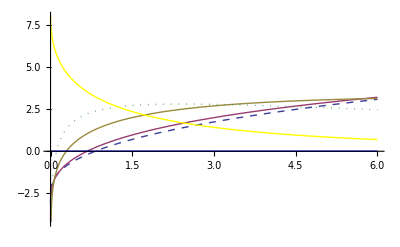

```mathematica
Plot[{
IFun[1,0.05],
IFun[1,0.1],
IFun[1,0.3],
IFun[1,0.5],
IFun[1,1],
IFun[1,2]},
{x,0,6},
PlotLegend->{"α = 0.05","α = 0.1","α = 0.3","α = 0.5","α = 1","α = 2"},
LegendPosition->{1,-0.4},
PlotStyle->{Dashed, Thick,Thin, Dotted, Yellow, Blue}
]
```

```mathematica
Weibull:
```

```mathematica
ClearAll[α,σ,μ,x]
```

```mathematica
p = k/λ ⅇ^(-((x-μ)/λ)^k)((x-μ)/λ)^(k-1)
```

(ⅇ^(-((x-μ)/λ)^k) k ((x-μ)/λ)^(-1+k))/λ

```mathematica
θ = μ;
```

```mathematica
ss = FullSimplify[D[Log[p],θ]]
```

(1+k (-1+((x-μ)/λ)^k))/(x-μ)

```mathematica
ss' = FullSimplify[D[ss,θ]]
```

-((-1+k) (1+k ((x-μ)/λ)^k))/(x-μ)^2

```mathematica
csIntCitatel1 = FullSimplify[p^(1+α)*ss]
```

((1+k (-1+((x-μ)/λ)^k)) ((ⅇ^(-((x-μ)/λ)^k) k ((x-μ)/λ)^(-1+k))/λ)^(1+α))/(x-μ)

```mathematica
csIntCitatel2 = FullSimplify[csIntCitatel1/.(x-μ)-> y*λ]
```

((1+k (-1+y^k)) ((ⅇ^(-y^k) k y^(-1+k))/λ)^(1+α))/(y λ)

```mathematica
csIntCitatel3 = FullSimplify[csIntCitatel2*λ/.y-> t^(1/k)]
```

t^(-1/k) (1+k (-1+(t^(1/k))^k)) ((ⅇ^(-(t^(1/k))^k) k (t^(1/k))^(-1+k))/λ)^(1+α)

```mathematica
csIntCitatel4 = FullSimplify[csIntCitatel3/k*t^((1-k)/k),{k>0,t>0,λ>0,α>0}]
```

ⅇ^(-t (1+α)) k^α (1+k (-1+t)) t^((-1+(-1+k) α)/k) λ^(-1-α)

```mathematica
csIntCitatel5 = FullSimplify[Integrate[csIntCitatel4,{t,0,∞}]]
```

ConditionalExpression[0,Re[(1+α-k α)/k]<1&&Re[α]>-1]

```mathematica
csIntJmenovatel1 = FullSimplify[p^(1+α)]
```

((ⅇ^(-((x-μ)/λ)^k) k ((x-μ)/λ)^(-1+k))/λ)^(1+α)

```mathematica
csIntJmenovatel2 = FullSimplify[csIntJmenovatel1/.(x-μ)-> y*λ]
```

((ⅇ^(-y^k) k y^(-1+k))/λ)^(1+α)

```mathematica
csIntJmenovatel3 = FullSimplify[csIntJmenovatel2*λ/.y-> t^(1/k)]
```

((ⅇ^(-(t^(1/k))^k) k (t^(1/k))^(-1+k))/λ)^(1+α) λ

```mathematica
csIntJmenovatel4 = FullSimplify[csIntJmenovatel3/k*t^((1-k)/k),{k>0,t>0,λ>0,α>0}]
```

ⅇ^-t ((ⅇ^-t k t^((-1+k)/k))/λ)^α

```mathematica
csIntJmenovatel5 = FullSimplify[Integrate[csIntJmenovatel4,{t,0,∞}]]
```

ConditionalExpression[(1+α)^(-1+(-1+1/k) α) (k/λ)^α Gamma[1+α-α/k],Re[(-1+1/k) α]<1&&Re[α]>-1]

```mathematica
cs = FullSimplify[csIntCitatel5/csIntJmenovatel5]
```

ConditionalExpression[0,Re[(-1+1/k) α]<1&&Re[(1+α-k α)/k]<1&&Re[α]>-1]

```mathematica
cs' = FullSimplify[D[cs,θ]]
```

ConditionalExpression[0,Re[(-1+1/k) α]<1&&Re[(1+α-k α)/k]<1&&Re[α]>-1]

```mathematica
Ia =FullSimplify[ (ss' - cs'-α(ss-cs)(cs-ss))*p^(1+α)]
```

ConditionalExpression[((α (1+k (-1+((x-μ)/λ)^k))^2-(-1+k) (1+k ((x-μ)/λ)^k)) ((ⅇ^(-((x-μ)/λ)^k) k ((x-μ)/λ)^(-1+k))/λ)^(1+α))/(x-μ)^2,Re[(-1+1/k) α]<1&&Re[(1+α-k α)/k]<1&&Re[α]>-1]

```mathematica
Ia1 = FullSimplify[Ia/.(x-μ)->y*λ]
```

ConditionalExpression[((-(-1+k) (1+k y^k)+(1+k (-1+y^k))^2 α) ((ⅇ^(-y^k) k y^(-1+k))/λ)^(1+α))/(y^2 λ^2),Re[(-1+1/k) α]<1&&Re[(1+α-k α)/k]<1&&Re[α]>-1]

```mathematica
Ia2 = FullSimplify[Ia1*λ/.y-> t^(1/k)]
```

ConditionalExpression[(t^(-2/k) (-(-1+k) (1+k (t^(1/k))^k)+(1+k (-1+(t^(1/k))^k))^2 α) ((ⅇ^(-(t^(1/k))^k) k (t^(1/k))^(-1+k))/λ)^(1+α))/λ,Re[(-1+1/k) α]<1&&Re[(1+α-k α)/k]<1&&Re[α]>-1]

```mathematica
Ia3 = FullSimplify[Ia2/k*t^((1-k)/k),{k>0,t>0,λ>0,α>0}]
```

ConditionalExpression[(ⅇ^-t t^(-2/k) (-(-1+k) (1+k t)+(1+k (-1+t))^2 α) ((ⅇ^-t k t^((-1+k)/k))/λ)^α)/λ^2,k>1]

```mathematica
Ia4 = FullSimplify[Integrate[Ia3,{t,0,∞}]]
```

ConditionalExpression[-(-1+k) k^α (1+α)^((2+α-k (3+α))/k) (-1+k+k α) (1/λ)^(2+α) Gamma[(-2+k+(-1+k) α)/k],k>1&&2+Re[α]<k+k Re[α]]

```mathematica
IFb = FullSimplify[-Ia4^(-1) * (p^α)*(ss-cs)]
```

ConditionalExpression[((1+α)^(-(2+α-k (3+α))/k) (1/λ)^(-2-α) (1+k (-1+((x-μ)/λ)^k)) ((ⅇ^(-((x-μ)/λ)^k) ((x-μ)/λ)^(-1+k))/λ)^α)/((-1+k) (-1+k+k α) (x-μ) Gamma[(-2+k+(-1+k) α)/k]),2+Re[α]<k+k Re[α]&&Re[(1+α-k α)/k]<1&&Re[α]>-1]

```mathematica
IF1b = FullSimplify[IFb/.λ->1]
```

ConditionalExpression[((1+α)^(-(2+α-k (3+α))/k) (1+k (-1+(x-μ)^k)) (ⅇ^(-(x-μ)^k) (x-μ)^(-1+k))^α)/((-1+k) (-1+k+k α) (x-μ) Gamma[(-2+k+(-1+k) α)/k]),2+Re[α]<k+k Re[α]&&Re[(1+α-k α)/k]<1&&Re[α]>-1]

```mathematica
IF2b = FullSimplify[IF1b/.k->2]
```

ConditionalExpression[((1+α)^(2+α/2) (-1+2 (x-μ)^2) (ⅇ^(-(x-μ)^2) (x-μ))^α)/((1+2 α) (x-μ) Gamma[α/2]),Re[α]>0]

```mathematica
IFun = Function[{μ,α} ,((1+α)^(2+α/2) (-1+2 (x-μ)^2) (ⅇ^(-(x-μ)^2) (x-μ))^α)/((1+2 α) (x-μ) Gamma[α/2])];
```

```mathematica
Needs["PlotLegends`"]
```

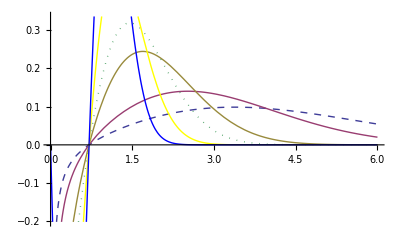

^6

```mathematica
Plot[{
IFun[0,0.05],
IFun[0,0.1],
IFun[0,0.3],
IFun[0,0.5],
IFun[0,1],
IFun[0,2]},
{x,0,6},
PlotLegend->{"α = 0.05","α = 0.1","α = 0.3","α = 0.5","α = 1","α = 2"},
LegendPosition->{1,-0.4},
PlotStyle->{Dashed, Thick,Thin, Dotted, Yellow, Blue}
]
```